# Лабораторная работа №3

## Нелинейные математические модели колебательных явлений

Мат. моделирование динамических процессов 1
БГУ, ММФ, 3 курс, 6 семестр
специальность Компьютерная математика и системный анализ
март 2022
ММФ, КМ и СА, доц. Лаврова О.А., доц. Щеглова Н.Л.
работу выполнил 
студент 3 курса 5 группы ММФ БГУ
Кирилло Дмитрий

## Задание 1. Математический маятник под действием силы тяжести без учета сопротивления среды

### Концептуальная постановка задачи

Объектом исследования является физическое тело массы m, которое подвешено на невесомом и нерастяжимом стержне длины l к неподвижной опоре. Тело имеет небольшие размеры по сравнению с длиной стержня, поэтому принимаем его за материальную точку.

Тело качается в фиксированной плоскости. Обозначим через α(t) угол отклонения стержня от вертикального положения равновесия α(t)=0. Будем считать, что α(t)>0 при отклонении стержня против часовой стрелки.

Тело находится под действием силы тяжести F̄=m ḡ; силой сопротивления среды пренебрегаем. Допущение об отсутствии трения справедливо для небольших промежутков времени.

```mathematica
g=QuantityMagnitude@WolframAlpha["Gravitational acceleration value", {{"Value", 1}, "QuantityData"}]
```

9.807

Принимая во внимание, что в момент времени t=0 стержень отклонили на угол α_0 и телу сообщили скорость ω_0, требуется определить угол отклонения стержня α(t) как функцию времени.

### Математическая модель

Математическая модель представляет собой задачу Коши для нелинейного однородного дифференциального уравнения второго порядка следующего вида

(ⅆ^2 α(t))/(ⅆ t^2)+g/l sin(α(t))==0,
α(0)=α_0,
(ⅆα(0))/ⅆt=ω_0.

```mathematica
DSolve[{a''[t]+g/l*Sin[a[t]]==0,a[0]==a0,a'[0]==w0},a[t],t]//Simplify (*1*)
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

DSolve::bvimp: General solution contains implicit solutions. In the boundary value problem, these solutions will be ignored, so some of the solutions will be lost.

{}

В случае малых колебаний маятника математическая модель (1) упрощается за счет допущения, что sin(α)≈α при α<<1 и сводится к модели гармонического осциллятора

(ⅆ^2 α(t))/(ⅆ t^2)+g/l α(t)==0,
α(0)=α_0,
(ⅆα(0))/ⅆt=ω_0.

```mathematica
DSolve[{a''[t]+g/l a[t]==0,a[0]==a0,a'[0]==w0},a[t],t]//Simplify (*2*)
```

{{a[t]→1. a0 Cos[(3.13161 t)/(√l)]+0.319324 √l w0 Sin[(3.13161 t)/(√l)]}}

### Задание 1.1 (Фазовый портрет)

На основании анализа уравнения фазовых траекторий сформулируйте выводы:

при каких ограничениях на начальные данные α_0 и ω_0 маятник находится в положении равновесия;

при каких ограничениях на начальные данные α_0 и ω_0 маятник совершает колебательные движения (замкнутые фазовые траектории);

при каких ограничениях на начальные данные α_0 и ω_0 маятник совершает вращательные движения (волнистые фазовые траектории);

при каких ограничениях на начальные данные α_0 и ω_0 фазовая траектория является сепаратрисой, т.е. разделяет колебательное и вращательное движение маятника.

Изобразите фазовые траектории динамической системы, соответствующей математической модели маятника, на фазовой плоскости переменных  α,ω:=(ⅆα(t))/ⅆt . Выделите цветом в фазовой плоскости четыре траектории, соответствующие разным типам движения маятника.

Запишем уравнение(ⅆ^2 α(t))/(ⅆ t^2)+g/l sin(α(t))=0  в виде динамической системы  относительно двух неизвестных: угла поворота α и 
угловой скорости ω. Тогда:

ⅆα/ⅆt= ω,  ⅆω/ⅆt=-g/lsin(α).

Как можно заметить, положение равновесия для динамической системы будут следующие:ω=0 и  α=πn, n∈ℤ .

На фазовой плоскости с координатами  α и ω имеем особые точки (πn,0), n∈ℤ, часть из которых являются устойчивыми. Построим дифференциальное уравнение фазовых траекторий:

ⅆω/ⅆα=-g/l(sin(α))/ω;

		ωⅆω=-g/lsin(α)ⅆα;

		ω^2/2=g/l cos(α)+const;

		ω^2=2 g/l cos(α)+const - уравнение фазовых траекторий.

Решением вышеприведенного уравнения является
		ω=±√(2(g/l cos(α)+const))

Фазовые траектории динамических систем:

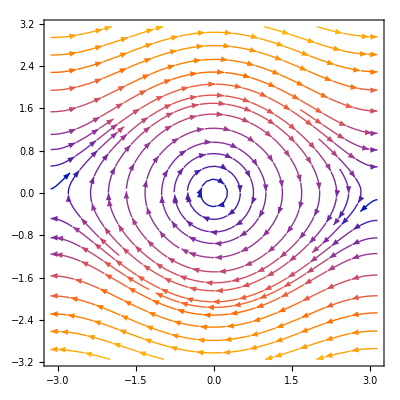

```mathematica
StreamPlot[{ω,-g/l Sin[α]},{α,-π,π},{ω,-π,π}]
```

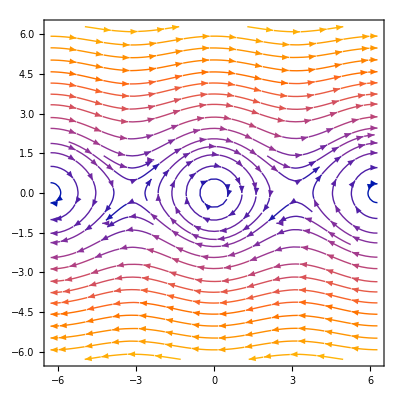

```mathematica
StreamPlot[{ω,-g/l Sin[α]},{α,-2π,2π},{ω,-2π,2π}]
```

Динамическая визуализация фазовых траекторий динамических систем:

```mathematica
Manipulate[{{TextCell[
If[Abs[const]<g/l,StringForm["TraditionalForm` | constTraditionalForm` | = ``<`` =g/l\n Колебательные движения",NumberForm[Abs[const],4],NumberForm[g/l,4]],
If[const>g/l,StringForm["const= ``>`` =g/l\n Вращательные движения",NumberForm[const,4],NumberForm[g/l,4]],
If[const==g/l,StringForm["const= ``=`` =g/l\n Сепаратриса",NumberForm[const,4],NumberForm[g/l,4]]]]
],
"Output"]},
{ContourPlot[{ω==√(2(g/l Cos[α]+const)),ω==-√(2(g/l Cos[α]+const))},{α,-2π,2π},{ω,-2π,2π},ImageSize->Medium]}},
{{l,1},0.1,10,0.1,Appearance->"Labeled"},
{{const,1},0,10,0.1,Appearance->"Labeled"}]
```

Как можно заметить из вышеприведенных графиков, разделим случаи, при которых маятник совершает разного рода движения:

 -- Колебательные движения (замкнутые фазовые траектории) -- для консервативных систем это соответствует незатухающим колебаниям. Данный случай возможен, когда |const| < g/l, то есть подкоренное выражение принимает как положительные, так и нулевые и отрицательные значения. Положение равновесия для данного случая являются точки, окруженными координатами (2πn, 0), n∈ ℤ.
 
 -- Вращательные движения (волнистые фазовые траектории) -- движение маятника, напоминающее в виде “волн”. Данный случай возможен в том случае, если const>g/l, то есть 2(g/l cos α+const) > 0.  Это означает то, что  колебательных движений у маятника будет отсутствовать, то есть направление маятника будет осуществляться строго в одном направлении. Следовательно, положения равновесия в данном случае не будет.
 
 -- Сепаратриса - фазовая траектория, разделяющая колебательное и вращательное движение маятника. Движение по сепаратрисе соответствует падению тела из положения равновесия α_0=π с нулевой начальной скоростью ω_0=0. Из дифференциального уравнения получаем, что данный случай наблюдается при const = g/l. Особые точки  являются ((2n+1)π,  0), n∈ ℤ. Стоит отметить, что из-за особенности сепаратрисы, фазовая плоскость разбивается на области, когда она является замкнутой фазовой траекторией (при колебательном движении) и незамкнутой, в случае волнистых фазовых траекторий (при вращательном движении). Соответственно, данный случай означает, что маятник принимает неустойчивое положение.
 
 Маятник находится в положении равновесия в случае, если ω = 0 и  α = π n, n∈ℤ . Причем на фазовой плоскости с координатами α и ω имеют особые точки (π n,0), 
 n∈ℤ, часть из которых являются устойчивыми. Также, при const = -g/l уравнение фазовых траекторий ω^2=2 g/l cos(α)+const будут принимать значения в точках, координаты которых  (2π n,0),  n∈ℤ. В данном случае, система будет устойчивой.
 
 Также, в предположении секундного маятника (в случае, если l∼ 1м),  мы получаем следующие случаи движения маятника:
 -- при |const| > g - маятник совершает вращательные движения  (волнистые фазовые траектории);
 -- при const < g - маятник совершает колебательные движения (замкнутые фазовые траектории);
 -- при const = g - сепаратриса (фазовая траектория, разделяющая колебательное и вращательное движение маятника),
    где const, из начальных условий, равна: const = ω_0^2/2 - g cos(α_0).

### Задание 1.2 (Динамическая визуализация)

Осуществите динамическую визуализацию поведения маятника для интерактивного задания параметров модели l>0, g>0,  α_0 и ω_0 с учетом трех режимов его движения: стационарный режим, колебательные движения, вращательные движения. 

В интерактивном объекте укажите  тип движения маятника на основании выводов из Задания 1.1.

```mathematica
Manipulate[{{TextCell[
If[Abs[Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]]]<g/l,StringForm["TraditionalForm` | (ω_0^2/2-g/l cos(α_0))TraditionalForm` | = ``<`` =g/l\n Колебательные движения",NumberForm[Abs[Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]]],4],NumberForm[g/l,4]],
If[(Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]])>g/l,StringForm["(ω_0^2/2-g/l cos(α_0))= ``>`` =g/l\n Вращательные движения",NumberForm[(Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]]),4],NumberForm[g/l,4]],
If[(Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]])==g/l,StringForm["(ω_0^2/2-g/l cos(α_0))= ``=`` =g/l\n Сепаратриса",NumberForm[(Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]]),4],NumberForm[g/l,4]],
If[Sin[Subscript[α, 0]]==0 &&Subscript[ω, 0]==0,Text["sin(α_0)= 0 и ω_0 = 0\n Стационарное положение"]]]
]
],
"Output"]},
{ContourPlot[{ω==√(2(g/l Cos[α]+(Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]]))),ω==-√(2(g/l Cos[α]+(Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]])))},{α,-2π,2π},{ω,-2π,2π},ImageSize->Medium]}},
{{l,1},0.1,10,0.1,Appearance->"Labeled"},
{{Subscript[ω, 0],π},-2π,2π,π/8,Appearance->"Labeled"},
{{Subscript[α, 0],π},-2π,2π,π/8,Appearance->"Labeled"}]
```

```mathematica
Quiet@Manipulate[{{TextCell[
If[Abs[Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]]]<g/l,StringForm["TraditionalForm` | (ω_0^2/2-g/l cos(α_0))TraditionalForm` | = ``<`` =g/l\n Колебательные движения",NumberForm[Abs[Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]]],4],NumberForm[g/l,4]],
If[(Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]])>g/l,StringForm["(ω_0^2/2-g/l cos(α_0))= ``>`` =g/l\n Вращательные движения",NumberForm[(Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]]),4],NumberForm[g/l,4]],
If[(Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]])==g/l,StringForm["(ω_0^2/2-g/l cos(α_0))= ``=`` =g/l\n Сепаратриса",NumberForm[(Subscript[ω, 0]^2/2-g/l Cos[Subscript[α, 0]]),4],NumberForm[g/l,4]],
If[Sin[Subscript[α, 0]]==0 &&Subscript[ω, 0]==0,Text["sin(α_0)= 0 и ω_0 = 0\n Стационарное положение"]]]
]
],
"Output"]},
{Animate[Show[
Graphics[{Thickness[0.01],Blue,Line[{{-1/50 l,0},{1/50 l,0}}]},PlotRange->1.5,ImageSize->300],Graphics[{Red,PointSize[0.03],Point[{-l Sin[sol[t]],-l Cos[sol[t]]}],
Thickness[0.01],Black,Line[{{0,0},{-l Sin[sol[t]],-l Cos[sol[t]]}}]
}]
],{t,0,sol⟦1,1,-1⟧}]}},
{{l,1},0.1,10,0.1,Appearance->"Labeled"},
{{Subscript[ω, 0],π},-2π,2π,π/8,Appearance->"Labeled"},
{{Subscript[α, 0],π},-2π,2π,π/8,Appearance->"Labeled"},
Button["Refresh data",sol=(α/. (NDSolve[{α''[t]+g/l Sin[α[t]]==0,α[0]==Subscript[α, 0],α'[0]==Subscript[ω, 0]},α,{t,0,Sqrt[l/g] 4 π}]⟦1,1⟧));
]
]
```

### Задание 1.3 (Период колебаний)

Постройте зависимость периода колебаний маятника T от начального угла α_0 вида T=T(α_0)=4 √(l/(2 g)) ∫_0^α_0 1/(√(cos(α)-cos(α_0)))ⅆα  в предположении, что начальная скорость равна нулю ω_0=0.  Найти значение периода можно из закона сохранения энергии, см. [1, стр. 44-45]. Альтетрнативный способ построения зависимости: 
 - умножить дифференциальное уравнения из математической модели (1) на α'(t);
 - проинтегрировать полученное уравнения по времени от момента времени t=0, что соответствует положению α=α_0 и начальной скорости ω_0=0, до момента времени t=T/4, что соответствует α=0.

Зависимость периода колебаний от начального угла T=T(α_0) является основной причиной того, что маятниковые часы не точные, так как тело  в крайнем положении отклоняется на угол, отличный от α_0 , см. [1, стр. 44-45].

Аналитическая зависимость периода колебаний маятника от начального угла может быть найдена также в базе знаний Wolfram Alpha

```mathematica
First@FormulaData[{"Pendulum", "Standard"}]
```

T Period==4 EllipticK[Sin[(θ_0 Angle)/2]^2] √((l Length)/(g GravitationalAcceleration))

В предположении о малых колебаниях маятника и без учета сопротивления среды период колебаний маятника T не будет зависеть от начальных данных. На основании математической модели (2) постройте зависимость периода колебаний T от параметров модели l и g. Определите длину стержня l для создания секундного маятника с периодом колебания T=2c.

```mathematica
SetDirectory@CurrentValue@"NotebookDirectory"
```

D:\ММДС

Решение задания определения длины стержня l для создания секундного маятника с периодом колебания T=2c:

```mathematica
Import["LR3T1.3T.pdf",{"PageImages",1}]
```

-Graphics-

Таким образом, период колебаний физического маятника зависит от угловой амплитуды колебаний α_0 . Этот факт и является причиной того, что колебания физического и математического маятников не изохронны, то есть маятниковые часы не являются точными, так как тело  в крайнем положении отклоняется на угол, отличный от α_0.
Интеграл в полученной формуле не может быть вычислен в элементарных функциях. Для его расчета используют табулированные функции эллиптических интегралов или численные методы.

Решение задания определения длины стержня l для создания секундного маятника с периодом колебания T=2c:

```mathematica
Import["LR3T1.3L.pdf",{"PageImages",1}]
```

-Graphics-

## Задание 2. Модель двухвидового взаимодействия “хищник-жертва”

Система уравнений Лотки-Вольтерра задает математическую модель взаимодействия популяции жертв с численностью N=N(t)≥0 и популяции хищников с численностью M=M(t)≥0

ⅆN/ⅆt==    α N - c N M,
ⅆM/ⅆt==-β M + d N M,
N(t_0)=N_0,
M(t_0)=M_0,

где 
α=const>0 -- коэффициент прироста жертв при отсутствии хищников в условиях неограниченности ресурса для питания; 
c=const>0 -- коэффициент пропорциональности при взаимодействии  жертв с хищниками, соответствующий уменьшению жертв; 
β=const>0 -- коэффициент смертности хищников при отсутствии жертв; 
d=const>0 -- коэффициент пропорциональности при взаимодействии  жертв с хищниками, соответствующий увеличению жертв.

### Задание 2.1 (Колебательное поведение)

Проиллюстрируйте существование колебательного поведения системы “хищник-жертва” в окрестности нетривиального положения равновесия N^*=β/d, M^*=α/c  по решению математической модели (3) и по фазовому портрету динамической системы. 

Решение необходимо построить численно, например, с помощью функции NDSolve. 

Продемонстрируйте  на фазовом портрете, что положение равновесия N^*=β/d, M^*=α/c является центром: окрестность положения равновесия (N^*,M^*) заполнена непересекающимися замкнутыми фазовыми траекториями, окружающими (N^*,M^*).

```mathematica
DSolve[{Ñ'[t]==α Ñ[t]-c Ñ[t] M̃[t],M̃'[t]==-β M̃[t]+d Ñ[t] M̃[t],Ñ[t0]==N0,M̃[t0]==M0},{Ñ[t],M̃[t]},t]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -M0+((InverseFunction[Power&][-t0 β+2])^(α/β))^(β/α) == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvsing: Unable to resolve some of the arbitrary constants in the general solution using the given boundary conditions. It is possible that some of the conditions have been specified at a singular point for the equation.

{{Ñ[t]→-1/dβ ProductLog[-1/βd ⅇ^((-c M0-d N0+c InverseFunction[1/(K[1] (1+ProductLog[-(d ⅇ^(-(c M0+d N0-β Log[M0^(α/β) N0])/β+(c K[1])/β) K[1]^(-α/β))/β]))K[1]1#1&][(-t+t0) β+1/(K[1] (1+ProductLog[-(d ⅇ^((-C[1]+c K[1])/β) K[1]^(-α/β))/β]))K[1]1M0])/β) M0^(α/β) N0 (InverseFunction[1/(K[1] (1+ProductLog[-(d ⅇ^(-(c M0+d N0-β Log[M0^(α/β) N0])/β+(c K[1])/β) K[1]^(-α/β))/β]))K[1]1#1&][(-t+t0) β+1/(K[1] (1+ProductLog[-(d ⅇ^((-C[1]+c K[1])/β) K[1]^(-α/β))/β]))K[1]1M0])^(-α/β)],M̃[t]→InverseFunction[1/(K[1] (1+ProductLog[-(d ⅇ^(-(c M0+d N0-β Log[M0^(α/β) N0])/β+(c K[1])/β) K[1]^(-α/β))/β]))K[1]1#1&][(-t+t0) β+1/(K[1] (1+ProductLog[-(d ⅇ^((-C[1]+c K[1])/β) K[1]^(-α/β))/β]))K[1]1M0]}}

Аналитическое исследование положения равновесия и особых точек математической модели (3):

```mathematica
Import["LR3T2.1.pdf",{"PageImages",1}]
```

-Graphics-

При N* = 0, M* = 0 особой точкой будет (0, 0), тогда, в таком случае, в нулевой момент времени животные обоих видов отсутствуют и дальше не появляются.

Рассмотрим ненулевой случай. В зависимости от начальных параметров будет меняться особая точка — такое значение размеров популяции животных, когда обе популяции остаются неизменными и сбалансированными. Если же начальное условие не попадает в особую точку, фазовые кривые будут идти вокруг нее, образуя бесконечное циклическое колебание. То есть количество особей одного вида будет расти, другого — падать, затем наоборот, и так в течение неограниченного количества времени.

{{Ñ[t]→InterpolatingFunction[{{0., 20.}}, <>][t],M̃[t]→InterpolatingFunction[{{0., 20.}}, <>][t]}}

{InterpolatingFunction[{{0., 20.}}, <>][t],InterpolatingFunction[{{0., 20.}}, <>][t]}

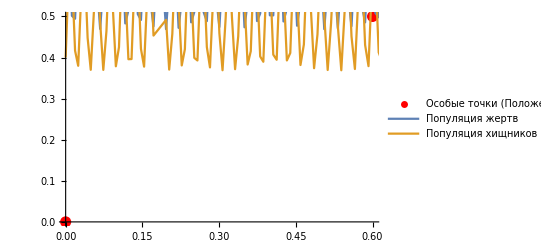

```mathematica
t0 =0;
t̃ =20;
N0= 3/5+1/10;
M0 = 1/2-1/10;
α=200;
β=300;
c=400;
d=500;

NDSolve[{Ñ'[t]==α Ñ[t]-c Ñ[t] M̃[t],M̃'[t]==-β M̃[t]+d Ñ[t] M̃[t],Ñ[t0]==N0,M̃[t0]==M0},{Ñ[t],M̃[t]},{t,t0 ,t̃}]
sol=Values@%//Flatten
Show[ListPlot[{{0,0},{β/d,α/c}},PlotStyle->{Red,PointSize[0.02]},PlotRange->Full,PlotLegends->{"Особые точки (Положения равновесия)"}],
Plot[{sol⟦1⟧,sol⟦2⟧},{t,t0 ,t̃},PlotLegends->{"Популяция жертв", "Популяция хищников"},Axes->True] ]
```

Как можно заметить из вышеприведенного графика, математическая модель «хищник-жертва» является колебательной.

```mathematica
Quiet@Manipulate[Show[Graphics[{Orange,PointSize[0.02],Point[{0,0}],Red,Point[{β/d,α/c}]}],
StreamPlot[{α NN-c NN MM,-β MM+d NN MM},{NN,0,50},{MM,0,50}],Axes->True],
{{α,60},1,100,1,Appearance->"Labeled"},
{{β,70},1,100,1,Appearance->"Labeled"},
{{c,20},1,100,1,Appearance->"Labeled"},
{{d,10},1,100,1,Appearance->"Labeled"}]
```

Из вышеприведенного фазового портрета можно заметить, что точка  N^*=β/d, M^*=α/c является фокусом фазового пространства.

### Задание 2.2 (Неявная зависимость между N(t) и M(t))

Постройте дифференциальное уравнение фазовых траекторий для математической модели (3) и, решая его, найдите неявную зависимость между численностями хищников и жертв в виде

-d N[t]+log(N[t]^β)-c M(t)+ln((M(t))^α)=C,

где значение неизвестной константы C определяется из начальных условий.

Решение задания 2.2:

```mathematica
Import["LR3T2.2.pdf",{"PageImages",1}]
```

-Graphics-

### Задание 2.3 (Структурная неустойчивость модели “хищник-жертва”)

Проиллюстрируйте структурную неустойчивость математической модели “хищник-жертва” (3). 

Для этого измените математическую модель (3) добавлением к правым частям произвольных слагаемых вида ϵ f(N,M), где ϵ<<1. Продемонстрируйте по фазовому портрету и по поведению решения для измененной математической модели, что изменяется качественное поведение системы уравнений Лотка-Вольтерра в окрестности нетривиального положения равновесия (N^*,M^*), т.е. что центр изменяется на другой тип особой точки. 

Для описания реальных процессов структурно-неустойчивые модели использовать нельзя!

ВНИМАНИЕ!!! СЛЕДУЮЩИЙ НИЖЕПРИВЕДЕННЫЙ КОНТЕНТ НЕ РЕКОМЕНДУЕТСЯ ДЛЯ ПРОСМОТРА СЛАБОНЕРВНЫМ!!!

Рассмотрим следующую систему уравнений Лотки-Вольтерра, которая задает математическую модель взаимодействия популяции жертв с численностью N=N(t)≥0 и популяции хищников с численностью M=M(t)≥0 , при котором учитывается миграция животных:

ⅆN/ⅆt==    α N - c N M +ϵ f_1(N,M),
ⅆM/ⅆt==-β M + d N M+ϵ f_2(N,M).

где ϵ << 1,
α=const>0 -- коэффициент прироста жертв при отсутствии хищников в условиях неограниченности ресурса для питания; 
c=const>0 -- коэффициент пропорциональности при взаимодействии  жертв с хищниками, соответствующий уменьшению жертв; 
β=const>0 -- коэффициент смертности хищников при отсутствии жертв; 
d=const>0 -- коэффициент пропорциональности при взаимодействии  жертв с хищниками, соответствующий увеличению жертв. 
Возьмем в качестве ϵ = 1/100,  f_1(N,M)= c/N, f_2(N,M)= d/M, то есть функции показывают отношение мигрирующих животных к общей массе. Для обоих случаев верно, что при положительных константах c, d особи будут прибывать в среду. Тогда система (4) примет следующий вид:

ⅆN/ⅆt==    α N - c N M +1/100 c/N,
ⅆM/ⅆt==-β M + d N M+1/100 d/M.

Особые точки:

```mathematica
ClearAll[α,Ñ,M̃,c,d,β ]
```

ClearAll::ssym: Ñ is not a symbol or a string.

ClearAll::ssym: M̃ is not a symbol or a string.

```mathematica
Solve[α Ñ-c Ñ M̃ + 1/100 c/(Ñ) ==0&&-β M̃+d Ñ M̃ +1/100 d/(M̃)==0,{ Ñ,M̃},Reals]
```

{{Ñ→ConditionalExpression[(-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]^2)/(100 d Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]^2), ],M̃→ConditionalExpression[Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1], ]},{Ñ→ConditionalExpression[(-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]^2)/(100 d Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]^2), ],M̃→ConditionalExpression[Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2], ]},{Ñ→ConditionalExpression[(-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]^2)/(100 d Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]^2), ],M̃→ConditionalExpression[Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3], ]},{Ñ→ConditionalExpression[(-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]^2)/(100 d Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]^2), ],M̃→ConditionalExpression[Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4], ]},{Ñ→ConditionalExpression[(-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]^2)/(100 d Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]^2), ],M̃→ConditionalExpression[Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5], ]}}

В данном случае мы берем особую точку, которая не является комплексным значением, так как, исходя из наших условий, N и M могут принимать значения особой точки только на множестве R, а не на множестве C. Тем более, на графике не получится изобразить точку с комплексным значением

Исследуем ситуацию на устойчивость: найдем якобиан и собственные значения:

```mathematica
J=({{α-c M̃, -c Ñ}, {d M̃, -β+d Ñ}}) ;
Det[J-λ IdentityMatrix[2]]/.Solve[α Ñ-c Ñ M̃ + 1/100 c/(Ñ) ==0&&-β M̃+d Ñ M̃ +1/100 d/(M̃)==0,{ Ñ,M̃},Reals]
Solve[(Det[J-λ IdentityMatrix[2]]/.Solve[α Ñ-c Ñ M̃ + 1/100 c/(Ñ) ==0&&-β M̃+d Ñ M̃ +1/100 d/(M̃)==0,{ Ñ,M̃},Reals])==0,λ]
```

{ConditionalExpression[-α β-α λ+β λ+λ^2+c β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]+c λ Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]+(α (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]^2)-(λ (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]^2), ],ConditionalExpression[-α β-α λ+β λ+λ^2+c β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]+c λ Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]+(α (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]^2)-(λ (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]^2), ],ConditionalExpression[-α β-α λ+β λ+λ^2+c β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]+c λ Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]+(α (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]^2)-(λ (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]^2), ],ConditionalExpression[-α β-α λ+β λ+λ^2+c β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]+c λ Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]+(α (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]^2)-(λ (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]^2), ],ConditionalExpression[-α β-α λ+β λ+λ^2+c β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]+c λ Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]+(α (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]^2)-(λ (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]^2), ]}

Solve::cndvs: The input to Solve should not contain conditionally valid subexpressions.

Solve[{ConditionalExpression[-α β-α λ+β λ+λ^2+c β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]+c λ Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]+(α (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]^2)-(λ (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,1]^2), ],ConditionalExpression[-α β-α λ+β λ+λ^2+c β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]+c λ Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]+(α (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]^2)-(λ (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,2]^2), ],ConditionalExpression[-α β-α λ+β λ+λ^2+c β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]+c λ Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]+(α (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]^2)-(λ (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,3]^2), ],ConditionalExpression[-α β-α λ+β λ+λ^2+c β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]+c λ Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]+(α (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]^2)-(λ (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,4]^2), ],ConditionalExpression[-α β-α λ+β λ+λ^2+c β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]+c λ Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]+(α (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]^2)-(λ (-d+100 β Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]^2))/(100 Root[-d^2 α+c d^2 #1+200 d α β #1^2-200 c d β #1^3+(-100 c d^2-10000 α β^2) #1^4+10000 c β^2 #1^5&,5]^2), ]}==0,λ]

В данном случае мы берем особую точку, которая не является комплексным значением, так как, исходя из наших условий, N и M могут принимать значения особой точки только на множестве R, а не на множестве C. Тем более, на графике не получится изобразить точку с комплексным значением

Построим фазовое пространство с особой точкой:

```mathematica
J=({{α-c M̃, -c Ñ}, {d M̃, -β+d Ñ}}) ;
Manipulate[{{Flatten@Values@Solve[(Det[J-λ IdentityMatrix[2]]/.Solve[α Ñ-c Ñ M̃ + 1/100 c/(Ñ) ==0&&-β M̃+d Ñ M̃ +1/100 d/(M̃)==0,{ Ñ,M̃},Reals])==0,λ]//N},
{Show[
Graphics[{PointSize[0.02],Red,Point[Flatten@Values@Solve[α Ñ-c Ñ M̃ + 1/100 c/(Ñ) ==0&&-β M̃+d Ñ M̃ +1/100 d/(M̃)==0,{ Ñ,M̃},Reals]]},ImageSize->Medium],StreamPlot[{α NN-c NN MM + 1/100 c/NN ,-β MM+d NN MM+1/100 d/MM},{NN,0,50},{MM,0,50}],Axes->True]}},
{{α,60},1,100,1,Appearance->"Labeled"},
{{β,70},1,100,1,Appearance->"Labeled"},
{{c,20},1,100,1,Appearance->"Labeled"},
{{d,10},1,100,1,Appearance->"Labeled"}]
```

Как можно заметить, значения λ выдают два значения. Это можно рассмотреть как λ = a ± iω, где a - первая часть слагаемого, на которую мы будем делать особенный акцент, а ω - подкоренной выражение, которое мы преобразуем так, чтобы получилось комплексное значение. Соответственно, если а = 0, то получаем особую точку типа центр, иначе — фокус. К тому же, если а < 0, то точка будет устойчивой, если a > 0 — неустойчивой. Таким образом, данная математическая модель является структурно неустойчивой.

Перейдем к более легкому случаю:

Рассмотрим следующую систему уравнений Лотки-Вольтерра, которая задает математическую модель взаимодействия популяции жертв с численностью N=N(t)≥0 и популяции хищников с численностью M=M(t)≥0 , при котором учитывается миграция животных:

ⅆN/ⅆt==    α N - c N M +ϵ f_1(N,M),
ⅆM/ⅆt==-β M + d N M+ϵ f_2(N,M).

где ϵ << 1,
α=const>0 -- коэффициент прироста жертв при отсутствии хищников в условиях неограниченности ресурса для питания; 
c=const>0 -- коэффициент пропорциональности при взаимодействии  жертв с хищниками, соответствующий уменьшению жертв; 
β=const>0 -- коэффициент смертности хищников при отсутствии жертв; 
d=const>0 -- коэффициент пропорциональности при взаимодействии  жертв с хищниками, соответствующий увеличению жертв. 
Возьмем в качестве ϵ = 1/100,  f_1(N,M)= c/N, f_2(N,M)= 0, то есть мы рассматриваем случай, когда мигрируют только жертвы. Тогда система (6) принимает следующий вид:

ⅆN/ⅆt==    α N - c N M +1/100 c/N,
ⅆM/ⅆt==-β M + d N M.

Особые точки:

```mathematica
Solve[α NN-c NN MM +1/100 c/NN ==0&&-β MM+d NN MM ==0,{ NN,MM}]
```

{{NN→-(ⅈ √c)/(10 √α),MM→0},{NN→(ⅈ √c)/(10 √α),MM→0},{NN→β/d,MM→(c d^2+100 α β^2)/(100 c β^2)}}

```mathematica
Flatten@Values@Solve[α NN-c NN MM +1/100 c/NN ==0&&-β MM+d NN MM ==0&&α>0&&β>0&&c>0&&d>0,{ NN,MM},Reals]
```

{ConditionalExpression[β/d, β>0&&α>0&&d>0&&c>0],ConditionalExpression[-(d^2 (-c-(100 α β^2)/d^2))/(100 c β^2), β>0&&α>0&&d>0&&c>0]}

```mathematica
Solve[α NN-c NN MM +1/100 c/NN ==0&&-β MM+d NN MM ==0,{ NN,MM}]⟦3⟧
```

{NN→β/d,MM→(c d^2+100 α β^2)/(100 c β^2)}

В данном случае мы берем особую точку, которая не является комплексным значением, так как, исходя из наших условий, N и M могут принимать значения особой точки только на множестве R, а не на множестве C. Тем более, на графике не получится изобразить точку с комплексным значением. То есть мы получаем случай, когда размеры популяций ненулевые.

```mathematica
J=({{α-c M̃, -c Ñ}, {d M̃, -β+d Ñ}}) ;
Det[J-λ IdentityMatrix[2]]/.{Ñ->β/d,M̃->(c d^2+100 α β^2)/(100 c β^2)}//Expand
Solve[(Det[J-λ IdentityMatrix[2]]/.{Ñ->β/d,M̃->(c d^2+100 α β^2)/(100 c β^2)})==0,λ]//Simplify
```

(c d^2)/(100 β)+α β+(c d^2 λ)/(100 β^2)+λ^2

{{λ→-(c d^2+√(c^2 d^4-400 c d^2 β^3-40000 α β^5))/(200 β^2)},{λ→(-c d^2+√(c^2 d^4-400 c d^2 β^3-40000 α β^5))/(200 β^2)}}

Как можно заметить, значения λ выдают два значения. Это можно рассмотреть как λ = a ± iω, где a - первая часть слагаемого, на которую мы будем делать особенный акцент, а ω - подкоренной выражение, которое мы преобразуем так, чтобы получилось комплексное значение. Соответственно, если а = 0, то получаем особую точку типа центр, иначе — фокус. К тому же, если а < 0, то точка будет устойчивой, если a > 0 — неустойчивой. Таким образом, данная математическая модель является структурно неустойчивой.

Построим фазовое пространство с особой точкой:

```mathematica
J=({{α-c M̃, -c Ñ}, {d M̃, -β+d Ñ}}) ;
Manipulate[{{Flatten@Values@Solve[(Det[J-λ IdentityMatrix[2]]/.(Solve[α Ñ-c Ñ M̃ + 1/100 c/(Ñ) ==0&&-β M̃+d Ñ M̃ ==0,{ Ñ,M̃}]⟦3⟧))==0,λ]//N},
{Show[
Graphics[{PointSize[0.02],Red,Point[Flatten@Values@Solve[α Ñ-c Ñ M̃ + 1/100 c/(Ñ) ==0&&-β M̃+d Ñ M̃ ==0,{ Ñ,M̃},Reals]]},ImageSize->Medium],StreamPlot[{α NN-c NN MM + 1/100 c/NN ,-β MM+d NN MM},{NN,0,50},{MM,0,50}],Axes->True]}},
{{α,60},1,100,1,Appearance->"Labeled"},
{{β,36},1,100,1,Appearance->"Labeled"},
{{c,4},1,100,1,Appearance->"Labeled"},
{{d,6},1,100,1,Appearance->"Labeled"}]
```

## Литература

[1] В. В. Амелькин. Дифференциальные уравнения в приложениях. -- М.: Наука, 1987.

[2] А. А. Андронов, А. А. Витт, С. Э. Хайкин. Теория колебаний. -- М.: Физматлит, 1959.